```mathematica
Задание 1.
```

```mathematica
A=RandomReal[{-10,10},{25,25}];
B=RandomReal[{-10,10},{25,25}];
```

```mathematica
A+=Transpose[A]; B+=Transpose[B];
```

```mathematica
{Det[A], Det[B]}
```

{1.55677×10^36,-5.41417×10^33}

```mathematica
Det[A-B]
```

-1.26128×10^39

```mathematica
P[A_,B_]:= MatrixPower[A+B,2]- Inverse[A].Transpose[B]-3*Det[B];
```

```mathematica
C1=P[A,B] ;
```

```mathematica
Cond = Norm[A, 2]*Norm[Inverse[A],2]
```

20.9612

```mathematica
Eigenvectors[C1]
```

{{-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2,-0.2},{-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,-0.0575914,0.0666351,0.0666351,0.0666351,0.0666351,-0.181818,-0.181818,-0.181818,0.834225,0.366151},{-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,-0.0110543,0.374575,0.374575,0.374575,0.374575,-0.325558,-0.325558,-0.325558,-0.344754,0.},{-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0208106,-0.0708604,-0.0708604,-0.0708604,-0.0708604,0.0292392,0.0292392,0.0292392,-0.380116,0.908809},{0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,0.136484,-0.245423,-0.245423,-0.245423,-0.245423,-0.391704,-0.391704,-0.391704,-0.0269429,0.},{-0.0279003,-0.0279003,-0.0200541,-0.0358365,0.0095026,0.00733071,0.00733071,0.00733071,0.00733071,0.00733071,0.0146001,0.0146001,0.00781714,0.00781714,0.00781714,0.0128835,0.000967732,0.000967732,-0.0139835,0.012048,-0.231265,-0.560775,0.79204,4.77386×10^-16,0.},{0.139038,0.139038,0.194882,0.119496,0.00264233,-0.000860203,-0.000860203,-0.000860203,-0.000860203,-0.000860203,-0.0225175,-0.0225175,-0.153498,-0.153498,-0.153498,-0.0852673,0.0345686,0.0345686,-0.0511382,-0.017999,0.705996,-0.549369,-0.156627,2.72678×10^-17,0.},{-0.318789,-0.318789,-0.565985,-0.125624,0.122923,0.120221,0.120221,0.120221,0.120221,0.120221,0.054032,0.054032,0.171551,0.171551,0.171551,-0.0175604,0.00742939,0.00742939,0.280291,-0.29515,0.270218,-0.176954,-0.0932637,-2.63678×10^-16,0.},{0.111201,0.111201,0.0120672,0.14271,0.155019,0.141679,0.141679,0.141679,0.141679,0.141679,-0.0783705,-0.0783705,-0.250576,-0.250576,-0.250576,-0.332126,-0.264223,-0.264223,0.589732,-0.0612849,-0.136098,0.0831114,0.0529864,3.41221×10^-17,0.},{0.206625,0.206625,-0.0026252,0.113926,-0.164093,0.0294578,0.0294578,0.0294578,0.0294578,0.0294578,-0.159645,-0.159645,0.0311209,0.0311209,0.0311209,-0.281819,0.360511,0.360511,-0.0469,-0.674121,-0.116548,0.0657104,0.0508378,-2.92662×10^-17,0.},{-0.0307406,-0.0307406,0.145696,-0.096808,0.0926418,-0.0668081,-0.0668081,-0.0668081,-0.0668081,-0.0668081,0.264502,0.264502,0.181285,0.181285,0.181285,-0.818867,-0.0299252,-0.0299252,-0.07866,0.13851,0.0161266,-0.00862817,-0.00749848,4.09191×10^-17,0.},{-0.00269894,-0.00269894,0.502513,-0.64736,-0.222252,-0.0278466,-0.0278466,-0.0278466,-0.0278466,-0.0278466,0.0530754,0.0530754,0.0799041,0.0799041,0.0799041,0.165866,-0.0634063,-0.0634063,0.382168,-0.255356,0.0477547,-0.0308325,-0.0169222,-8.97608×10^-17,0.},{-0.200688,-0.200688,0.0868535,-0.294133,-0.12212,0.252291,0.252291,0.252291,0.252291,0.252291,0.191119,0.191119,-0.275741,-0.275741,-0.275741,-0.0856949,0.160033,0.160033,-0.350938,0.0308717,-0.0599274,0.068751,-0.00882364,1.05958×10^-17,0.},{-0.363099,-0.363099,0.433907,0.277825,0.547771,-0.0933031,-0.0933031,-0.0933031,-0.0933031,-0.0933031,0.0346326,0.0346326,-0.0739766,-0.0739766,-0.0739766,0.0858748,0.110132,0.110132,0.0464704,-0.266734,-0.0464138,0.0351981,0.0112156,-2.83963×10^-17,0.},{0.276248,0.276248,-0.240793,-0.504962,0.683314,-0.0562586,-0.0562586,-0.0562586,-0.0562586,-0.0562586,0.00615577,0.00615577,-0.0876216,-0.0876216,-0.0876216,0.0417912,0.0753316,0.0753316,-0.117136,-0.0335269,-0.014167,0.0195752,-0.00540819,-3.25319×10^-17,0.},{0.106406,0.106406,-0.226009,0.160234,-0.177406,-0.145917,-0.145917,-0.145917,-0.145917,-0.145917,0.540083,0.540083,-0.159974,-0.159974,-0.159974,0.159708,0.0252303,0.0252303,0.165424,-0.215885,-0.0337934,0.0218881,0.0119053,-1.39968×10^-17,0.},{-0.00601904,0.00601904,6.66134×10^-16,-1.66533×10^-16,-6.245×10^-16,0.239892,0.00974332,-0.313452,-0.14916,0.212976,-0.0123915,0.0123915,0.258827,0.0365206,-0.295348,-6.10623×10^-16,-0.557029,0.557029,-8.25829×10^-16,5.93718×10^-16,2.06107×10^-16,-8.40325×10^-17,9.8913×10^-17,-7.14328×10^-17,0.},{-0.0790808,0.0790808,-3.05311×10^-16,4.996×10^-16,-1.2837×10^-15,0.162223,-0.424552,-0.274364,-0.0157439,0.552437,-0.0496221,0.0496221,0.26588,0.00870024,-0.27458,8.04912×10^-16,0.352941,-0.352941,8.01494×10^-16,-2.37676×10^-16,8.77902×10^-18,1.61964×10^-17,7.1661×10^-17,9.52675×10^-17,0.},{0.110047,-0.110047,-7.49401×10^-16,-3.44169×10^-15,6.52256×10^-15,0.173206,0.620272,-0.33576,-0.143178,-0.314539,-0.00880446,0.00880446,0.202655,0.168668,-0.371323,3.05311×10^-16,0.24629,-0.24629,-6.94269×10^-16,-1.20399×10^-15,-1.00583×10^-16,1.1465×10^-16,-1.07301×10^-16,2.195×10^-17,0.},{-0.0209112,0.0209112,-1.0842×10^-16,-1.17441×10^-15,2.3589×10^-15,0.381368,-0.0553819,-0.43698,0.33596,-0.224966,-0.344641,0.344641,-0.0377671,-0.339201,0.376968,-6.74807×10^-16,0.00465754,-0.00465754,-4.04529×10^-16,-2.25835×10^-16,1.36244×10^-17,2.38977×10^-17,-2.35656×10^-17,3.49495×10^-17,0.},{0.0591813,-0.0591813,3.1225×10^-16,2.21698×10^-15,-4.05839×10^-15,-0.306041,-0.184872,0.204421,0.57952,-0.293028,-0.144865,0.144865,0.43335,-0.0251072,-0.408243,7.5287×10^-16,-0.0479743,0.0479743,7.43788×10^-16,4.17774×10^-16,1.1151×10^-17,-2.30798×10^-17,3.93353×10^-17,-1.3556×10^-17,0.},{-0.260839,0.260839,-4.51028×10^-17,-9.45424×10^-17,2.00577×10^-16,-0.363586,0.318326,-0.226327,0.121368,0.150219,0.273209,-0.273209,0.322927,-0.505015,0.182088,-1.5439×10^-16,0.00757679,-0.00757679,-6.25522×10^-17,2.7632×10^-17,1.43186×10^-18,1.60333×10^-17,1.7189×10^-17,-4.1866×10^-17,0.},{0.0103655,-0.0103655,-1.02349×10^-16,5.96745×10^-16,-1.35308×10^-15,-0.452326,0.295997,0.0702677,-0.245963,0.332024,-0.514458,0.514458,0.00366705,-0.0340951,0.030428,2.70617×10^-16,-0.0151767,0.0151767,1.46465×10^-16,2.4357×10^-16,2.31514×10^-17,-2.43273×10^-17,2.1981×10^-17,-2.38308×10^-17,0.},{0.0784625,-0.0784625,-1.17961×10^-16,-9.95731×10^-16,1.24206×10^-15,0.298546,-0.0931545,0.445795,-0.474125,-0.177062,-0.0523792,0.0523792,0.439344,-0.480651,0.0413076,-6.8695×10^-16,0.0433552,-0.0433552,-3.60918×10^-16,-6.50696×10^-17,2.40535×10^-18,-8.68262×10^-18,-3.16735×10^-17,-2.31118×10^-17,0.},{0.635106,-0.635106,1.31188×10^-17,5.63785×10^-16,-8.5427×10^-16,-0.145291,-0.00742949,-0.161566,0.09093,0.223356,0.124456,-0.124456,0.037109,-0.184098,0.146989,1.35525×10^-16,-0.00138078,0.00138078,1.41418×10^-16,1.47535×10^-16,-6.10339×10^-18,-6.14951×10^-18,2.0276×10^-17,9.60162×10^-18,0.}}

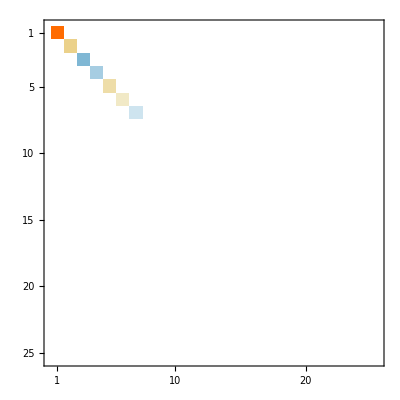

```mathematica
DiagonalMatrix[Eigenvalues[C1]] // MatrixPlot
```

```mathematica
Задание 2.
```

```mathematica
a1 = {3,-2,2,7}; a2= {-2,0,2,3}; a3={5,-2,0,4}; a4={1,-2,4,11};
```

```mathematica
A=Transpose[{a1,a2,a3,a4}];
```

```mathematica
A // RowReduce // MatrixForm
```

(1 | 0 | 1 | 0
0 | 1 | -1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
Линейнонезависимы a1, a2, a4
```

```mathematica
b1 = a1; b2= a2; b3= RandomInteger[{-5, 5}, {1,4}][[1]]; b4= a4;
```

```mathematica
({c1,c2,c3,c4}=Orthogonalize[{b1,b2,b3,b4}]) // MatrixForm
```

(√(3/22) | -√(2/33) | √(2/33) | 7/(√66)
-63 √(3/16742) | 19 √(2/25113) | 47 √(2/25113) | 65/(√50226)
-745 √(2/8490477) | -1147 √(3/5660318) | -1703/(√16980954) | 71 √(2/8490477)
-11 √(2/11157) | 23 √(3/7438) | -115/(√22314) | 31 √(2/11157))

```mathematica
Задание 3.
```

```mathematica
f=(2+x)^3;
```

```mathematica
{e1, e2, e3, e4}=Orthogonalize[{1,x,x^2,x^3},Integrate[#1 #2,{x,-1,1}]&]
```

{1/(√2),√(3/2) x,3/2 √(5/2) (-1/3+x^2),5/2 √(7/2) (-(3 x)/5+x^3)}

```mathematica
Integrate[e1*f,{x,-1,1}]
```

10 √2

```mathematica
Integrate[e2*f,{x,-1,1}]
```

(21 √6)/5

```mathematica
Integrate[e3*f,{x,-1,1}]
```

4 √(2/5)

```mathematica
Integrate[e4*f,{x,-1,1}]
```

(2 √(2/7))/5

```mathematica
Задание 4.
```

```mathematica
A4=({{1, 2, 3, -2}, {2, -1, -2, -3}, {3, 2, -1, 2}, {2, -3, 2, 1}});
```

```mathematica
bb4 = {6,8,4,-8};
```

```mathematica
x=Inverse[A4].bb4
```

{1,2,-1,-2}

```mathematica
Cond4=Norm[A4, 2]* Norm[Inverse[A4],2]
```

1

```mathematica
{lu, p , c} =LUDecomposition[A4]
```

{{{1,2,3,-2},{3,-4,-10,8},{2,5/4,9/2,-9},{2,7/4,3,18}},{1,3,2,4},0}

```mathematica
Задание 5.
```

```mathematica
h=1/10; n=IntegerPart[10/h];
```

```mathematica
c=Table[-2/h^2,{i, 2, n}]; d=Table[1/h^2,{i, 1, n-1}]; b= Table[1/h^2,{i, 2, n}];
PrependTo[c,1]; AppendTo[c,1];
PrependTo[d,0];
AppendTo[b,0];
```

```mathematica
A5=DiagonalMatrix[c]+DiagonalMatrix[d, 1]+ DiagonalMatrix[b,-1] ;
```

```mathematica
f= Table[Sin[i*h], {i,1,n-1}]; PrependTo[f,1]; AppendTo[f,-1];
```

```mathematica
Solve
```

```mathematica
{timeSolve, xSlv}= AbsoluteTiming[LinearSolve[A5,f]];
```

```mathematica
Algorythm
```

```mathematica
alg[bb_,cc_,dd_, ff_]:=Module[{dels,lams, X, b,c,d,f},f=ff; d=dd; c= cc; b=Prepend[bb,0];dels=(RecurrenceTable[{dell[i]==-Indexed[d,i]/(Indexed[b,i]*dell[i-1]+Indexed[c,i]),dell[1]==-d[[1]]/c[[1]]},dell,{i,1,n,1}]//N);lams=RecurrenceTable[{lam[1]==f[[1]]/c[[1]],lam[i]==(Indexed[f,i]-Indexed[b, i]*lam[i-1])/(Indexed[b,i]*Indexed[dels, i-1]+Indexed[c,i])},lam,{i,1,n,1}];
X=RecurrenceTable[{x[1]==(f[[n+1]]-b[[n+1]]*lams[[n]])/(b[[n+1]]*dels[[n]] + c[[n+1]]),x[j]== Indexed[dels,n+2-j]*x[j-1]+Indexed[lams,n+2-j]},x,{j,1,n+1,1}];
Reverse[X]]
```

```mathematica
{timeAlg, X} =AbsoluteTiming[alg[b,c,d,f]];
```

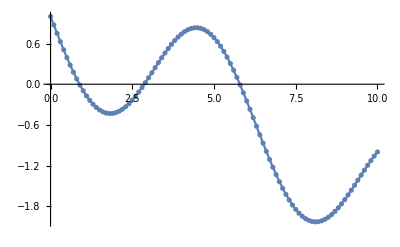

```mathematica
Show[ListPlot[X, DataRange->{0,10}],Plot[(10-2x+x*Sin[10]-10*Sin[x])/10,{x,0,10}]]
```

```mathematica
timeAlg
```

0.00940445

```mathematica
timeSolve
```

18.6615